## Definition

```mathematica
colorrules =  {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]};
```

```mathematica
nonzeroRange[list_]:= SparseArray[list]["NonzeroPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
tofunc[bitfuncspec_, k_] := Which[
IntegerQ[bitfuncspec], bitfuncspec&,
bitfuncspec ==="Random", (RandomChoice[Delete[Range[0, k - 1], #+1]]&),
bitfuncspec[[1]] ==="AddValue", (Mod[(# + bitfuncspec[[2]]), k] &),
True, (bitfuncspec[#, k]&)]
```

```mathematica
totmax[txspec_]:= Replace[txspec, {
 t_Integer:> t,
{tspec_, xspec___}:> Replace[tspec, {
t_Integer ||{t_Integer}||{{t_Integer}}:> t,
{t1_Integer, t2_Integer} || {t1_Integer, t2_Integer, dt_Integer}:> t2}]}]
```

```mathematica
totrange[txspec_]:= Replace[txspec, {
 i_Integer:> All,
{tspec_, xspec___}:> Replace[tspec, {
t_Integer:> All,
 {t_Integer}:> {t},{{t_Integer}}:> t,
{t1_Integer, t2_Integer}:> t1;;t2 ,{t1_Integer, t2_Integer, dt_Integer}:> t1;;t2;;dt}]}]
```

```mathematica
interpretrule[rule_] := Replace[rule, {
   n_Integer :> {n, 2, 1},
   List[n_Integer, k_Integer] :>  {n, k, 1},
   List[n_Integer, k_Integer, r_?NumberQ] :> {n, k, r},
   List[n_Integer, k_Integer, r_?NumberQ, s_Integer] :> {n, k, r},
   List[n_Integer, List[k_Integer, 1]] :> {n, k, 1},
   List[n_Integer, List[k_Integer, 1], r_?NumberQ] :> {n, k, r}
   }]
```

```mathematica
expandrange[idxspec_, t_]:= If[t == 0, {}, Replace[idxspec,{
i_Integer:> {i},
{is__} :> {is},
Span[s_, e_] :> Range[s, If[e === All, t, e]], 
f_:> (If[IntegerQ[#], {#}, #]&)[f[Range[t]]]
}]]
```

```mathematica
tosingle[{is_, j_}->r_]:= {#, j}->r&/@is
```

```mathematica
ClearAll@tofullform
```

```mathematica
tofullform[idxspec_, t_] := 
 Composition[
   Catenate[tosingle/@#]&,
   MapAt[expandrange[#, t] &, #, Table[{i, 1, 1}, {i, Length[#]}]] &,
   If[! MatchQ[#, _Rule], # -> "Random", #] & /@ # &, 
   Replace[#, Rule[idxs_, val_] :> (# -> val & /@ idxs)] &,
   Replace[#, {
      {ispec_, jspec_} /; (! ListQ[ispec]) :> {{ispec, jspec}},
      Rule[{ispec_, jspec_}, b_] /; (! ListQ[ispec]) :> ({{ispec, jspec} -> b})
      }] &][idxspec]
```

```mathematica
PerturbedArrayPlot[{ca_, pert_}, ops:OptionsPattern[]]:=
ArrayPlot[ca,ops, Epilog->({Arrowheads[Large], 
Arrow[{{0, Length[ca] - #1 + .5},{#2-.5 ,Length[ca] - #1 +.5}}]&@@@Keys[pert]})]
```

```mathematica
ClearAll@PerturbedCellularAutomaton
```

```mathematica
Options[PerturbedCellularAutomaton] = {"ReturnPerturbations"->True, "Body"->False};
```

```mathematica
PerturbedCellularAutomaton[ru_, init_, txspec_, ops:OptionsPattern[]]:= PerturbedCellularAutomaton[ru, init, txspec, 1, ops]
PerturbedCellularAutomaton[ru_, init_, txspec_, idxspec_Integer, ops:OptionsPattern[]]:= PerturbedCellularAutomaton[ru, init, txspec, {{RandomChoice[#, idxspec] &, RandomChoice}}, Sequence@@Normal[Merge[{{"Body"->True}, ops}, Last]]]
PerturbedCellularAutomaton[ru_, init_, txspec_, idxspec_Integer->b_, ops:OptionsPattern[]]:= PerturbedCellularAutomaton[ru, init, txspec, {{RandomChoice[#, idxspec] &, RandomChoice} -> b}, Sequence@@Normal[Merge[{{"Body"->True}, ops}, Last]]]
```

```mathematica
PerturbedCellularAutomaton[ru_,init_:{{1}, 0}, txspec_:200, idxspec_:1, OptionsPattern[PerturbedCellularAutomaton]]:= Module[{},
k = interpretrule[ru][[2]];
tmax = totmax[txspec];
 tpert = If[OptionValue["Body"],ca = CellularAutomaton[ru, init, txspec];If[# == -Infinity, Length[ca], #]&[TestCALifeTime[ca]], tmax];
trange = totrange[txspec];
fullidxs = SortBy[tofullform[Normal[idxspec], tpert], #[[1, 1]]&];
pre = If[OptionValue["Body"], ca[[;;fullidxs[[1, 1, 1]]]],CellularAutomaton[ru, init,fullidxs[[1, 1, 1]]]];
ts = Differences[Append[fullidxs[[All, 1, 1]],  tmax+1]];
indexfunc = If[OptionValue["Body"],If[# == {}, {}, Range@@#]&[nonzeroRange[#]]&, Range[Length[#]]&];
evoca[{preca_, prepert_}, {{i1_, j1_}->bitfunc_,tcurr_}]:=Module[{},
row = Last[preca];
rowidxs = indexfunc[row];expanded = Select[expandrange[j1, Length[rowidxs]], #<= Length[rowidxs]&];
rowinrange = rowidxs[[expanded]];
{CellularAutomaton[ru, replaced = ReplacePart[row,#->tofunc[bitfunc, k][row[[#]]]&/@rowinrange],tcurr],
If[# == {},{i1, {}}->None, #]&[Thread[Thread[{i1,rowinrange}]-> replaced[[rowinrange]]]]}];
caperts = FoldList[evoca, {pre, {}},Transpose[{fullidxs, ts}]];
pca = Join@@(Most/@caperts[[All, 1]]);
If[OptionValue["ReturnPerturbations"],{pca[[trange]],  Association[Cases[caperts[[2;;, 2]], _Rule, 2]]},
 pca[[trange]]]]
```

```mathematica
GraphicsRow[{ArrayPlot[CellularAutomaton[30, {{1}, 0}, 50], ColorRules->None], CAMask[CellularAutomaton[30, {{1}, 0}, 50]]}]
```

-Graphics-

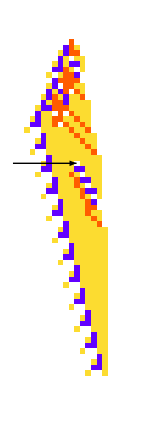

```mathematica
PerturbedArrayPlot[PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1}, {{1}, 0}, {65, {-10, 10}}]]
```

```mathematica
With[{ca = First[#]},ArrayPlot[ca, ColorRules->colorrules, Epilog->(Arrow[{{0, Length[ca] - #1},{#2,Length[ca] - #1}}]&@@@Keys[Last[#]])]]&[PerturbedCellularAutomaton[{297413941736400589979939780692294751544,4,1}, {{1}, 0}, {200, {-50, 50}},{100, 15}]]
```

## Documentation

### Basic Examples

Run a cellular automaton for 2 steps, with a random perturbation, here the second cell of the second row is flipped to 1:

```mathematica
PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1},{{1},0},2]
```

{{{0,0,1,0},{0,1,1,3}},<|{2,2}→1|>}

```mathematica
PerturbedCellularAutomaton[{297413946807002990892857386679107573048,4,1},{{1},0},2, 2]
```

{{{0,0,1,0},{0,2,1,3}},<|{3,3}→2,{3,1}→1|>}

```mathematica
PerturbedCellularAutomaton[30,{{1},0},2, {2, 1}]
```

{{{0,0,1,0,0},{0,0,1,1,0}},<|{2,2}→0|>}

We can specify the number of random perturbations like so:

```mathematica
PerturbedCellularAutomaton[30,{{1},0},2, 2]
```

{{{0,0,0,0,0},{0,0,1,0,0},{0,1,1,1,0}},<|{1,3}→0,{2,3}→1|>}

```mathematica
js
```

{2,3,4}

```mathematica
PerturbedCellularAutomaton[30,{{1},0},2, {2, 1}->0]
```

{{{0,0,1,0,0},{0,0,1,1,0},{0,1,1,0,1}},<|{2,2}→0|>}

```mathematica
MapAt[ArrayPlot, PerturbedCellularAutomaton[30,{{1},0},2, {2, 1}->0], 1]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

CellularAutomaton::initn: The initial condition specification {0,0[1,2],1,1,0} should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

Join::heads: Heads List and CellularAutomaton at positions 1 and 2 are expected to be the same.

ArrayPlot::mat: Argument Join[{{0,0,1,0,0}},CellularAutomaton[30,{0,0[1,2],1,1,0}]] at position 1 is not a list of lists.

{ArrayPlot[Join[{{0,0,1,0,0}},CellularAutomaton[30,{0,0[1,2],1,1,0}]]],<|{2,2}→{0,0[1,2],1,1,0}|>}

```mathematica
MapAt[ArrayPlot, PerturbedCellularAutomaton[30,{{1},0},2, 2, ],1]
```

MapAt::psl: Position specification {3,3}→1 in MapAt[ArrayPlot,{{{0,0,1,0,0},{0,1,1,0,0},{1,1,1,1,0}},<|{2,4}→0,{3,3}→1|>},{3,3}→1] is not a machine-sized integer or a list of machine-sized integers.

MapAt[ArrayPlot,{{{0,0,1,0,0},{0,1,1,0,0},{1,1,1,1,0}},<|{2,4}→0,{3,3}→1|>},{3,3}→1]

Run rule 30 for 2 steps, with a random perturbation, here the third body cell of the first row is flipped to white:

```mathematica
fullidxs
```

{{1,RandomChoice}→Random,{3,RandomChoice}→Random}

```mathematica
indexfunc[row]
```

{}

```mathematica
getidxs[3, ]
```

RandomChoice[{}]

```mathematica
PerturbedCellularAutomaton[30,{{1},0},2, 2]
```

RandomChoice::lrwl: The items for choice {} should be a non-empty list or a rule weights -> choices.

RandomChoice::lrwl: The items for choice {}→1 should be a non-empty list or a rule weights -> choices.

ReplacePart::reps: RandomChoice[{}→1] is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

CellularAutomaton::initn: The initial condition specification ReplacePart[{0,0,0,0,0},RandomChoice[{}→1]] should be of the form aspec, {aspec, bspec}, or {{{aspec1, off1}, {aspec2, off2},... {aspecn, offn}}, bspec} (n > 0). Each aspec must be a non-empty rank 1 array whose elements at level 1 are integers i in the range 0 <= i <= 1.

Join::heads: Heads List and CellularAutomaton at positions 1 and 3 are expected to be the same.

Part::partw: Part 3 of {} does not exist.

CellularAutomaton::argb: CellularAutomaton called with 0 arguments; between 1 and 3 arguments are expected.

{Join[{},{{0,0,0,0,0},{0,0,0,0,0}},CellularAutomaton[30,ReplacePart[{0,0,0,0,0},RandomChoice[{}→1]]]],<|{1,3}→Join[{},{{0,0,0,0,0},{0,0,0,0,0}},CellularAutomaton[30,ReplacePart[{0,0,0,0,0},RandomChoice[{}→1]]]]⟦1,3⟧,{3,{}}→CellularAutomaton[]|>}

```mathematica
ArrayPlot[First[PerturbedCellularAutomaton[30,{{1},0},50]]]
```

-Graphics-

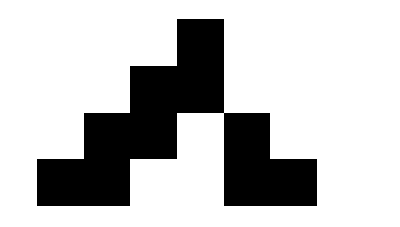

```mathematica
PerturbedCellularAutomaton[30, {{1}, 0}, 3] // ArrayPlot[First[#]]&
```

### Scope

One perturbation from the left of the non-zero range of the second row:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,2->"Left"]
```

{{0,0,0,1,0,0,0},{0,0,1,2,2,0,0},{0,2,0,1,1,0,0},{0,0,0,2,1,2,0}}

Three perturbations from the right of the non-zero range:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,2->{"Right", 3}]
```

{{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,2,2,2,0},{0,0,0,1,2,1,0}}

All perturbations from the left:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,2->{"Left", All}]
```

{{0,0,0,1,0,0,0},{0,0,0,1,1,0,0},{0,0,2,2,1,2,0},{0,0,1,0,2,2,0}}

The third and fifth number from the center:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,2->{"Center", {3, 5}}]
```

{{0,0,0,1,0,0,0},{0,0,2,2,0,0,0},{0,0,1,1,0,0,0},{0,2,2,1,2,0,0}}

The third through fifth number from the left:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,2->{"Left", {{3, 5}}}]
```

{{0,0,0,1,0,0,0},{0,0,2,2,0,0,0},{0,0,1,1,0,0,0},{0,2,2,1,2,0,0}}

You can also just specify the regular index ignoring the color range like so, here just perturbing the first number in the second row

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,{2, 1}]
```

{{0,0,0,1,0,0,0},{1,0,2,2,2,0,0},{2,2,1,2,1,0,2},{2,0,2,1,0,2,1}}

One perturbation at the second row, the CA is evolved and then another perturbation at the third row. The list of successive CAs is returned:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,{2->1, 3->1}]
```

{{{0,0,0,1,0,0,0},{0,0,2,2,2,0,0},{0,0,1,2,1,0,0},{0,2,0,1,0,2,0}},{{0,0,0,1,0,0,0},{0,0,2,2,0,0,0},{0,0,1,1,0,0,0},{0,2,2,1,2,0,0}},{{0,0,0,1,0,0,0},{0,0,2,2,0,0,0},{0,0,1,2,0,0,0},{0,2,0,2,0,0,0}}}

A random perturbation followed by a right perturbation

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,{2->1, 3->"Right"}]
```

{{{0,0,0,1,0,0,0},{0,0,2,2,2,0,0},{0,0,1,2,1,0,0},{0,2,0,1,0,2,0}},{{0,0,0,1,0,0,0},{0,0,0,2,2,0,0},{0,0,0,1,1,0,0},{0,0,2,2,1,2,0}},{{0,0,0,1,0,0,0},{0,0,0,2,2,0,0},{0,0,0,1,2,0,0},{0,0,2,0,2,0,0}}}

You can also specify indices in the list, ignoring the color range. Here the seventh number in the third index is perturbed:

```mathematica
PerturbedCAEvolution[{5586032021307, 3, 1}, {{1}, 0}, 3,{2->1,{3, 7}}]
```

{{{0,0,0,1,0,0,0},{0,0,2,2,2,0,0},{0,0,1,2,1,0,0},{0,2,0,1,0,2,0}},{{0,0,0,1,0,0,0},{0,0,2,0,2,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,1,0,0,0},{0,0,2,0,2,0,0},{0,0,0,0,0,0,1},{2,0,0,0,0,2,2}}}

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples